ⅇ^(4 ⅈ (12+x)-1/16 (12+x)^2)

2 √2 ⅇ^(-4 (16-(8+3 ⅈ) p+p^2))

Piecewise[{{2 √2 ⅇ^(-4 (16-(8+3 ⅈ) p+p^2)), 7/2≤p≤9/2}, {0, True}}]

1/2 ⅇ^(-1/16 (12+x) ((12-64 ⅈ)+x)) (Erf[(1+3 ⅈ)+(ⅈ x)/4]-ⅈ Erfi[(3+ⅈ)+x/4])

Piecewise[{{2 √2 ⅇ^(-4 (16-(8+3 ⅈ) p+p^2)), p≤7/2||p≥9/2}, {0, True}}]

1/2 ⅇ^(-1/16 (12+x) ((12-64 ⅈ)+x)) (1+Erfc[(1+3 ⅈ)+(ⅈ x)/4]+ⅈ Erfi[(3+ⅈ)+x/4])

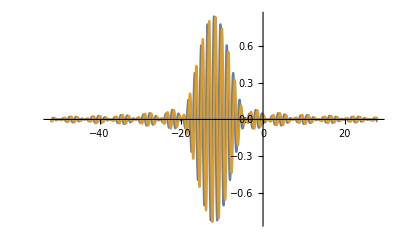

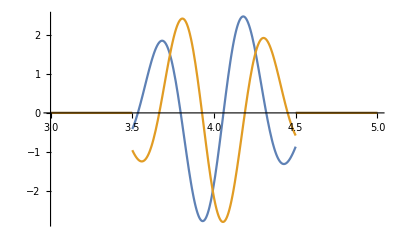

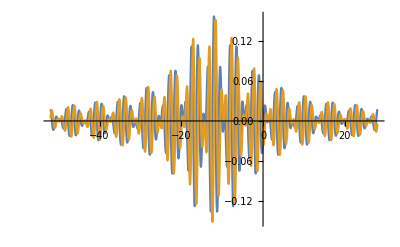

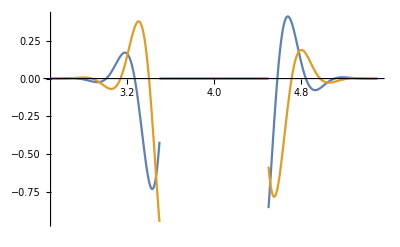

```mathematica
ћ=1;
a=4;
x0=-12;
p0=4;
pRange=1;
ψ=Exp[-((x-x0)/a)^2+ⅈ p0 (x-x0)/ћ]
ϕ=InverseFourierTransform[ψ,x,p]
ϕ1=Piecewise[{{ϕ,p0-pRange/2≤p≤p0+pRange/2}}]
ψ1=FourierTransform[ϕ1,p,x]
ϕ2=Piecewise[{{ϕ,p≤p0-pRange/2},{ϕ,p≥p0+pRange/2}}]
ψ2=FourierTransform[ϕ2,p,x]
Plot[{Re[ψ1],Im[ψ1]},{x,x0-40,x0+40},PlotRange->All,PlotPoints->150]
Plot[{Re[ϕ1],Im[ϕ1]},{p,p0-pRange/2-1/2,p0+pRange/2+1/2},PlotRange->All,PlotPoints->150]
Plot[{Re[ψ2],Im[ψ2]},{x,x0-40,x0+40},PlotRange->All,PlotPoints->150]
Plot[{Re[ϕ2],Im[ϕ2]},{p,-6/a+p0,6/a +p0},PlotRange->All,PlotPoints->150]
```